```mathematica
Quit[];
```

```mathematica
SetOptions[{Plot,LogPlot, LogLogPlot,ParametricPlot},{Frame->True,FrameStyle->Black,ImageSize->Large,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"],PlotStyle->AbsoluteThickness[3]}];
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot,ListLinePlot},{Frame->True,FrameStyle->Black,ImageSize->Large,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"],PlotStyle->AbsoluteThickness[3],Joined->True}];
Color[1]=RGBColor["#5E81B5"];
Color[2]=RGBColor["#E19C24"];
Color[3]=RGBColor["#8FB032"];
Color[4]=RGBColor["#EB6235"];
Color[5]=RGBColor["#8778B3"];
Color[6]=RGBColor["#C56E1A"];
```

```mathematica
mx=0.1;
R=1/9;
my=R mx;
U[x_]:=1/2 mx^2 x^2;
V[y_]:=1/2 my^2 y^2;
W[x_,y_]:=U[x]+V[y];
xin=13;
yin=13;
H[x_,y_,p_,q_]:=Sqrt[(1/2 p^2+1/2 q^2+W[x,y])/3];
Hend=Sqrt[0.03 mx^2/3]
sol=NDSolve[{x'[n]==p[n]/H[x[n],y[n],p[n],q[n]],p'[n]==-3p[n]-U'[x[n]]/H[x[n],y[n],p[n],q[n]],y'[n]==q[n]/H[x[n],y[n],p[n],q[n]],q'[n]==-3q[n]-V'[y[n]]/H[x[n],y[n],p[n],q[n]],x[0]==xin,y[0]==yin,p[0]==0,q[0]==0},{x,y,p,q},{n,0,90}][[1]];
phi=x/.sol;
psi=y/.sol;
pi=p/.sol;
chi=q/.sol;
```

0.01

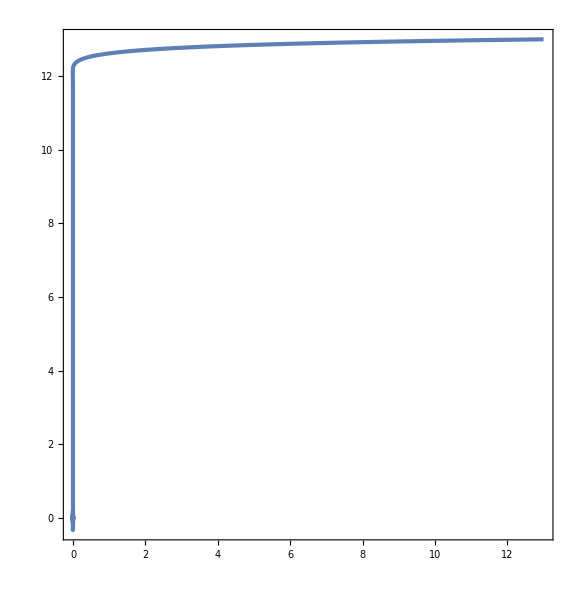

```mathematica
ParametricPlot[{phi[n],psi[n]},{n,0,90}]
```

```mathematica
Hcl[n_]=H[phi[n],psi[n],pi[n],chi[n]];
ϵH[n_]=1/2(pi[n]^2+chi[n]^2)/Hcl[n]^2;
```

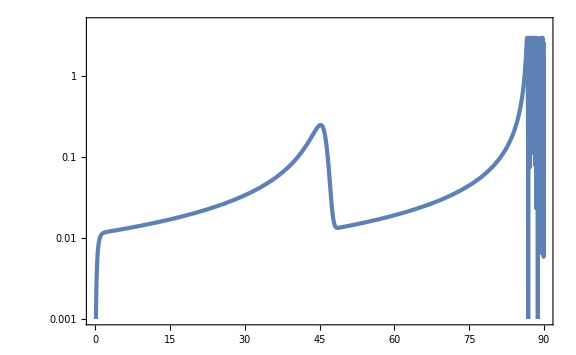

```mathematica
LogPlot[ϵH[n],{n,0,90}]
```

```mathematica
𝒫ζ[n_]=1/(24 π^2)W[phi[n],psi[n]]/ϵH[n];
```

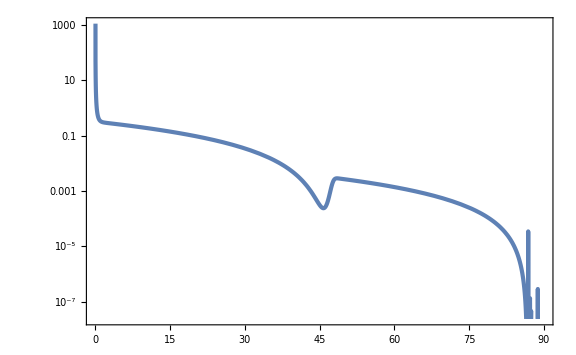

```mathematica
LogPlot[𝒫ζ[n],{n,0,90}]
```

```mathematica
Nend=n/.FindRoot[H[x[n]/.sol,y[n]/.sol,p[n]/.sol,q[n]/.sol]==Hend,{n,86}]
```

85.1052

```mathematica
phic=x[Nend]/.sol
psic=y[Nend]/.sol
```

-4.91451×10^-10

2.06448

```mathematica
Uc=U[phic];
Vc=V[psic];
Upc=U'[phic];
Vpc=V'[psic];
Uppc=U''[phic];
Vppc=V''[psic];
xcx[x_]=1/U'[x](Upc Vpc^2)/(Upc^2+Vpc^2);
xcy[y_]=-1/V'[y](Upc Vpc^2)/(Upc^2+Vpc^2);
ycx[x_]=-1/U'[x](Upc^2 Vpc)/(Upc^2+Vpc^2);
ycy[y_]=1/V'[y](Upc^2 Vpc)/(Upc^2+Vpc^2);
xbxback[x_,Ns_]=U'[phi[Ns]]/(U'[x]W[phi[Ns],psi[Ns]])((Uc Vpc^2-Vc Upc^2)/(Upc^2+Vpc^2)+V[psi[Ns]]);
xbyback[y_,Ns_]=U'[phi[Ns]]/(V'[y]W[phi[Ns],psi[Ns]])((Vc Upc^2-Uc Vpc^2)/(Upc^2+Vpc^2)-V[psi[Ns]]);
ybxback[x_,Ns_]=V'[psi[Ns]]/(U'[x]W[phi[Ns],psi[Ns]])((Uc Vpc^2-Vc Upc^2)/(Upc^2+Vpc^2)-U[phi[Ns]]);
ybyback[y_,Ns_]=V'[psi[Ns]]/(V'[y]W[phi[Ns],psi[Ns]])((Vc Upc^2-Uc Vpc^2)/(Upc^2+Vpc^2)+U[phi[Ns]]);
xbxfor[x_,Ns_]=U'[phi[Ns]]/U'[x](U[x]+V[psi[Ns]])/W[phi[Ns],psi[Ns]];
xbyfor[y_,Ns_]=U'[phi[Ns]]/V'[y](V[y]-V[psi[Ns]])/W[phi[Ns],psi[Ns]];
ybxfor[x_,Ns_]=V'[psi[Ns]]/U'[x](U[x]-U[phi[Ns]])/W[phi[Ns],psi[Ns]];
ybyfor[y_,Ns_]=V'[psi[Ns]]/V'[y](V[y]+U[phi[Ns]])/W[phi[Ns],psi[Ns]];
Nx[x_]=U[x]/U'[x]-Vc/Vpc ycx[x]-Uc/Upc xcx[x];
Ny[y_]=V[y]/V'[y]-Vc/Vpc ycy[y]-Uc/Upc xcy[y];
Nxx[x_]=1-U''[x]/U'[x]^2(U[x]+(Vc Upc^2-Uc Vpc^2)/(Upc^2+Vpc^2))+1/U'[x]^2(Upc^2 Vpc^2)/((Upc^2+Vpc^2)^2)(2(Uppc Vc+Uc Vppc)-Upc^2-Vpc^2+2(Uppc+Vppc)(Uc Vpc^2-Vc Upc^2)/(Upc^2+Vpc^2));
Nyy[y_]=1-V''[y]/V'[y]^2(V[y]+(Uc Vpc^2-Vc Upc^2)/(Upc^2+Vpc^2))+1/V'[y]^2(Upc^2 Vpc^2)/((Upc^2+Vpc^2)^2)(2(Uppc Vc+Uc Vppc)-Upc^2-Vpc^2+2(Uppc+Vppc)(Uc Vpc^2-Vc Upc^2)/(Upc^2+Vpc^2));
Nxy[x_,y_]=2/(U'[x]V'[y])(Upc^2 Vpc^2)/((Upc^2+Vpc^2)^2)(Upc^2+Vpc^2-2(Uppc Vc+Uc Vppc)+2(Uppc+Vppc)(Vc Upc^2-Uc Vpc^2)/(Upc^2+Vpc^2));
𝒫ζδN[n_]=(Nx[phi[n]]^2+Ny[psi[n]]^2)(Hcl[n]/(2π))^2;
```

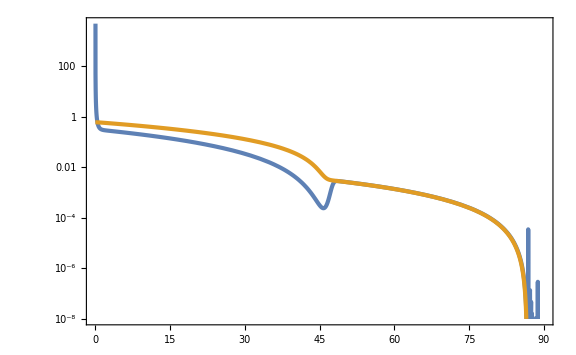

```mathematica
LogPlot[{𝒫ζ[n],𝒫ζδN[n]},{n,0,90}]
```

```mathematica
Px[x_,y_]=1/(6 π^2)((Nx[x]Nxx[x]+Ny[y]Nxy[x,y])W[x,y]+1/2(Nx[x]^2+Ny[y]^2)U'[x]);
Py[x_,y_]=1/(6 π^2)((Ny[y]Nyy[y]+Nx[x]Nxy[x,y])W[x,y]+1/2(Nx[x]^2+Ny[y]^2)V'[y]);
fNLback[Nl_,Ns_]=1/(W[phi[Ns],psi[Ns]]/(3 π^2)(Nx[phi[Ns]]^2+Ny[psi[Ns]]^2)(Nx[phi[Nl]]^2+Ny[psi[Nl]]^2))(Nx[phi[Nl]](Px[phi[Ns],psi[Ns]]xbxback[phi[Nl],Ns]+Py[phi[Ns],psi[Ns]]ybxback[phi[Nl],Ns])+Ny[psi[Nl]](Px[phi[Ns],psi[Ns]]xbyback[psi[Nl],Ns]+Py[phi[Ns],psi[Ns]]ybyback[psi[Nl],Ns]));
fNLfor[Nl_,Ns_]=1/(W[phi[Ns],psi[Ns]]/(3 π^2)(Nx[phi[Ns]]^2+Ny[psi[Ns]]^2)(Nx[phi[Nl]]^2+Ny[psi[Nl]]^2))(Nx[phi[Nl]](Px[phi[Ns],psi[Ns]]xbxfor[phi[Nl],Ns]+Py[phi[Ns],psi[Ns]]ybxfor[phi[Nl],Ns])+Ny[psi[Nl]](Px[phi[Ns],psi[Ns]]xbyfor[psi[Nl],Ns]+Py[phi[Ns],psi[Ns]]ybyfor[psi[Nl],Ns]));
```

```mathematica
Ni[1][Nl_]=Nx[phi[Nl]];
Ni[2][Nl_]=Ny[psi[Nl]];
Nij[1][1][Nl_]=Nxx[phi[Nl]];
Nij[1][2][Nl_]=Nxy[phi[Nl],psi[Nl]];
Nij[2][1][Nl_]=Nxy[phi[Nl],psi[Nl]];
Nij[2][2][Nl_]=Nyy[psi[Nl]];
Wi[1][Nl_]=U'[phi[Nl]];
Wi[2][Nl_]=V'[psi[Nl]];
WW[Nl_]=W[phi[Nl],psi[Nl]];
```

```mathematica
nsnum[Nl_]=1+𝒫ζδN'[Nl]/𝒫ζδN[Nl];
nsanal[Nl_]=1-1/Sum[(Ni[k][Nl])^2,{k,2}] Sum[(Wi[i][Nl])/WW[Nl](2Ni[j][Nl]Nij[i][j][Nl]+Ni[j][Nl]Ni[j][Nl](Wi[i][Nl])/WW[Nl]),{i,2},{j,2}];
nsapprox[Nl_]=1-4/(phi[Nl]^2+psi[Nl]^2)(1+((phi[Nl]^2+psi[Nl]^2)(mx^4 phi[Nl]^2+my^4 psi[Nl]^2))/((mx^2 phi[Nl]^2+my^2 psi[Nl]^2)^2));
```

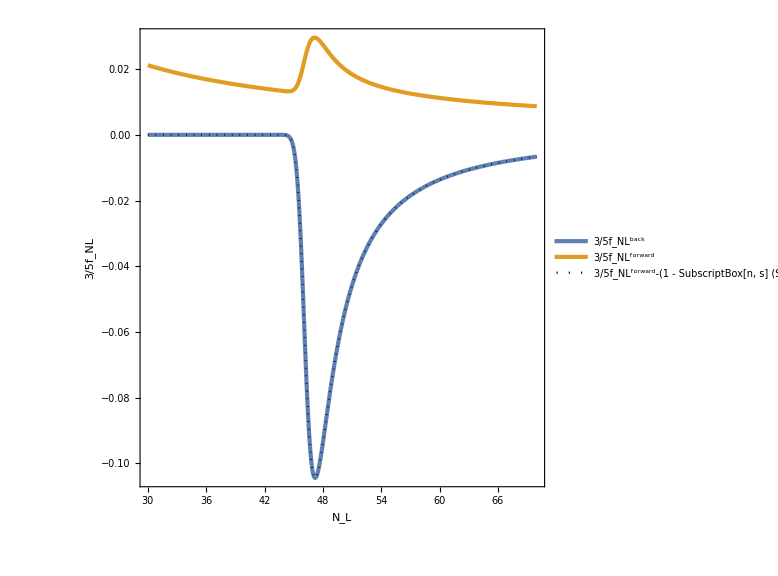

```mathematica
Plot[{fNLback[Nend-Nl,Nend-Nl+7],fNLfor[Nend-Nl,Nend-Nl+7],fNLfor[Nend-Nl,Nend-Nl+7]-(1-nsanal[Nend-Nl+7])/4},{Nl,30,70},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],{Black,Dotted}},FrameLabel->{{"3/5f_NL",None},{Subscript[N, L],Subscript[N, S]==Subscript[N, L]-7}},PlotLegends->Placed[LineLegend[{"3/5f_NL^back","3/5f_NL^forward","3/5f_NL^forward-(1 - SubscriptBox[n, s] (SubscriptBox[k, S]))/4"},LabelStyle->Directive[FontSize->20,FontFamily->"Palatino"],LegendMarkerSize->20],{0.77,0.2}],AspectRatio->1]
```

```mathematica
fNLequil[n_]=1/(phi[n]^2+psi[n]^2)(1-((phi[n]^2+psi[n]^2)(phi[n]^2+R^4 psi[n]^2))/((phi[n]^2+R^2 psi[n]^2)^2));
```

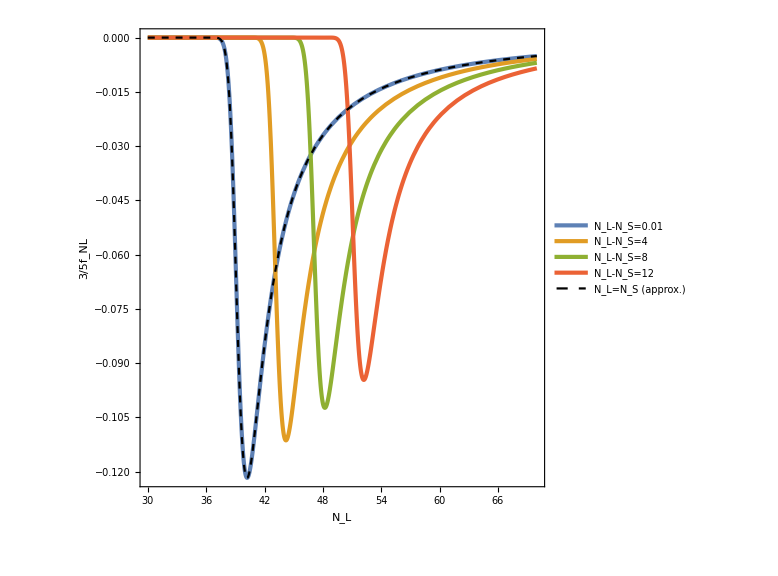

```mathematica
Plot[{fNLback[Nend-Nl,Nend-Nl+0.01],fNLback[Nend-Nl,Nend-Nl+4],fNLback[Nend-Nl,Nend-Nl+8],fNLback[Nend-Nl,Nend-Nl+12],fNLequil[Nend-Nl]},{Nl,30,70},PlotRange->Full,FrameLabel->{{"3/5f_NL",None},{Subscript[N, L],None}},AspectRatio->1,PlotLegends->Placed[LineLegend[{"N_L-N_S=0.01","N_L-N_S=4","N_L-N_S=8","N_L-N_S=12","N_L=N_S (approx.)"},LabelStyle->Directive[FontSize->14,FontFamily->"Palatino"],LegendMarkerSize->20],{0.8,0.25}],PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],AbsoluteThickness[3],{Black,Dashed}}]
```

```mathematica
fNLe[x_,y_,r_]=1/(x^2+y^2)(1-((x^2+y^2)(x^2+r^4 y^2))/((x^2+r^2 y^2)^2));
```

```mathematica
Plot3D[Abs[fNLe[x,y,0.1]],{x,1,100},{y,1,100},ImageSize->Large,LabelStyle->Large]
```

-Graphics3D-